## BoundedCellVoronoi-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.5 (6-Nov-2012)) loaded Thu 8 Nov 2012 18:36:01
using xCellerator 0.90 and XSSA 1204002

Cellzilla2D (2.0.α.1 (21-Jun-09)) loaded Sun 21 Jun 2009 17:20:55 using xlr8r 0.74 (13 May 2009)

Generate 50 random vertices to use a Voronoi Centers

```mathematica
r:=RandomReal[{0,100}]; 
v=Table[{r,r}, {50}];
```

Use the Voronoi Centers to generate a tissue with 50 cells using the Bounded-Cell-Voronoi algorithm

```mathematica
w=BoundedCellVoronoi[v]
```

Tissue[{{-8.57563,48.6167},{-8.33245,90.3246},{-6.77805,38.6989},{-6.4566,93.4063},{-4.1794,76.9081},{-4.17167,75.9546},{-1.48649,34.3501},{-0.888884,60.4644},{-0.707913,62.1447},{0.0309667,27.7155},{1.1306,97.4739},{1.84915,25.922},{1.89252,66.5058},{1.95704,66.7295},{1.98445,14.711},{2.22512,23.7629},{3.46719,97.4594},{5.24255,39.8568},{5.27462,98.5986},{5.82815,88.9485},{6.06951,50.0057},{6.52611,9.57618},{8.79337,102.503},{10.876,20.0742},{13.7654,47.8431},{14.2384,104.298},{15.4398,73.4653},{16.1132,38.8355},{16.1953,8.18416},{16.2371,8.43731},{18.2355,6.04546},{18.5751,5.96368},{19.2141,20.1446},{19.3623,80.0937},{19.3968,80.6218},{19.5519,53.1496},{21.3935,85.543},{23.506,102.439},{23.5829,102.533},{24.7516,31.4835},{24.8184,31.0093},{24.8952,31.9453},{25.3604,91.4134},{26.5245,53.419},{27.6533,34.6565},{28.0511,35.567},{28.2053,-1.25718},{28.9061,24.7882},{29.1566,41.428},{29.3366,58.9298},{32.0989,107.314},{32.2075,75.6746},{32.3613,15.9827},{33.9347,-1.1692},{36.4327,78.8226},{37.2704,64.5902},{37.3993,62.0782},{37.8784,89.7563},{38.5258,-6.96792},{39.139,107.233},{40.0438,10.5178},{40.6047,23.0222},{42.4517,91.1728},{42.4864,11.2061},{43.6577,76.3975},{43.7819,29.7583},{44.1381,15.5525},{46.8197,-8.88881},{46.9532,8.97513},{47.375,40.5402},{48.5845,100.527},{48.9757,100.618},{49.1597,30.1525},{49.3244,78.9098},{49.9666,78.63},{51.4309,52.6191},{51.5546,-5.82653},{52.5594,54.1485},{52.7557,55.9347},{52.9651,55.3587},{53.73,26.8998},{54.1962,26.8667},{55.0949,99.4508},{56.4506,88.9528},{58.2633,39.6845},{58.5318,70.9421},{58.9678,24.6624},{60.1387,100.381},{60.1428,-5.51164},{61.1269,-6.3961},{62.8751,11.239},{63.446,99.3254},{65.1735,13.8502},{69.222,76.5205},{69.8642,76.7047},{69.9828,77.1221},{70.5912,35.838},{70.7546,13.6605},{71.7116,100.99},{72.1971,74.9768},{72.4093,49.8866},{74.3934,12.5175},{74.7812,37.754},{75.2576,-6.65201},{75.4496,36.6074},{76.7776,47.1043},{78.2325,98.0628},{81.6454,92.3316},{82.1098,49.4339},{83.8999,4.8852},{83.9516,2.09189},{84.0569,28.5887},{84.5028,70.2919},{86.1301,61.8001},{86.8695,91.3395},{89.3374,-3.79399},{90.3964,46.3399},{90.5175,61.3437},{92.1483,85.9165},{94.4767,77.5217},{95.0018,77.3766},{96.4768,26.4441},{98.8977,16.626},{99.5816,24.1889},{99.959,22.7468},{101.818,49.2931},{102.71,71.3045},{103.819,49.6487},{103.851,-5.76619},{103.899,61.4956},{104.886,65.7643},{105.335,9.50468},{105.518,55.2759},{105.926,-3.63886},{107.075,45.0418},{107.692,35.37}},{{1,3},{1,8},{2,4},{2,5},{3,7},{4,11},{5,6},{5,20},{6,14},{7,10},{7,18},{8,9},{8,21},{9,13},{10,12},{11,17},{12,16},{12,40},{13,14},{13,36},{14,27},{15,16},{15,22},{16,24},{17,19},{17,20},{18,21},{18,28},{19,23},{19,37},{20,35},{21,25},{22,29},{23,26},{24,30},{24,33},{25,28},{25,36},{26,38},{27,34},{27,50},{28,42},{29,30},{29,31},{30,33},{31,32},{32,47},{32,53},{33,41},{34,35},{34,52},{35,37},{36,44},{37,43},{38,39},{38,43},{39,51},{40,41},{40,42},{41,48},{42,45},{43,58},{44,49},{44,50},{45,46},{45,66},{46,49},{46,70},{47,54},{48,53},{48,62},{49,76},{50,57},{51,60},{52,55},{52,56},{53,61},{54,59},{54,61},{55,58},{55,65},{56,57},{56,65},{57,79},{58,63},{59,68},{60,71},{61,64},{62,66},{62,67},{63,71},{63,74},{64,67},{64,69},{65,74},{66,73},{67,81},{68,77},{69,77},{69,91},{70,73},{70,76},{71,72},{72,83},{73,81},{74,75},{75,84},{75,86},{76,78},{77,89},{78,80},{78,85},{79,80},{79,86},{80,101},{81,82},{82,85},{82,87},{83,84},{83,88},{84,94},{85,97},{86,94},{87,93},{87,97},{88,92},{89,90},{89,91},{90,104},{91,93},{92,96},{92,99},{93,98},{94,95},{95,96},{95,100},{96,108},{97,103},{98,102},{98,105},{99,107},{100,101},{100,113},{101,106},{102,110},{102,112},{103,105},{103,106},{104,111},{105,112},{106,109},{107,108},{108,115},{109,114},{109,117},{110,111},{110,123},{111,116},{112,122},{113,114},{113,120},{114,118},{115,119},{116,129},{117,122},{117,126},{118,126},{118,130},{119,120},{120,121},{121,127},{122,124},{123,125},{123,132},{124,125},{124,136},{126,128},{127,131},{128,133},{128,135},{129,134},{130,131},{130,133},{132,134},{135,136}},{{52,50,51,75,80,62,54},{59,58,60,71,89,66,61},{80,81,95,92,85},{64,63,72,109,111,113,84,73},{112,122,138,148,144,115,111},{79,78,86,98,99,94,88},{7,9,21,40,50,31,8},{91,92,106,107,119,104,103},{119,121,134,135,131,126,120},{155,166,167,162,154},{118,125,122,117},{19,20,53,64,41,21},{17,24,36,49,58,18},{65,66,96,101,68},{97,93,94,100,130,124,118,116},{156,158,164,181,184,174,157},{123,114,113,115,142,136,134},{47,69,79,77,48},{131,137,152,141,132},{177,179,183,168,167},{28,37,32,27},{144,151,154,160,143,142},{23,33,43,35,24,22},{12,13,32,38,20,14},{76,83,81,75},{10,15,18,59,42,28,11},{128,127,129,149,156,145,139,133,130},{6,3,4,8,26,16},{38,37,42,61,65,67,63,53},{55,56,62,85,91,87,74,57},{1,5,11,27,13,2},{67,68,102,72},{166,165,172,176,185,180,177},{135,136,143,161,169,163,153,137},{70,77,88,93,90,71},{83,82,84,114,108,106,95},{139,146,150,140},{145,157,173,175,172,159,146},{45,43,44,46,48,70,60,49},{125,124,133,140,147,138},{41,73,82,76,51,40},{102,101,105,116,117,112,109},{108,123,121,107},{26,31,52,30,25},{29,30,54,56,39,34},{148,147,150,159,165,155,151},{35,45,36},{160,162,168,182,178,171,170,161},{89,90,97,105,96},{99,110,128,100}}]

Show the tissue and the centers

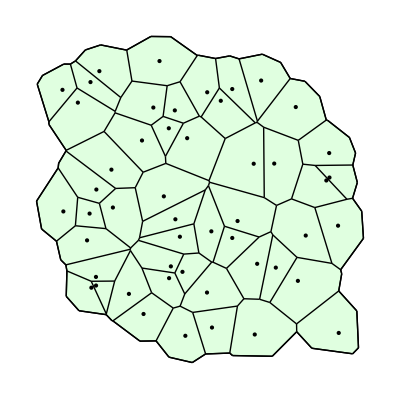

```mathematica
ShowTissue[w, Epilog-> Point/@v]
```